# Example of NIntegrate with Principal Value

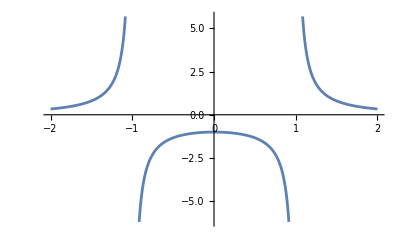

```mathematica
Plot[1/(x^2-1),{x,-2,2}]
```

```mathematica
NIntegrate[1/(x^2-1),{x,-2,2},Method->"PrincipalValue",Exclusions->{x==1,x==-1}]
Integrate[+I π DiracDelta[x-1]/2+I π DiracDelta[x+1]/2,{x,-2,2}] 
val=Integrate[1/(x^2-1),x]
(val/.x->2)-(val/.x->-2)//N
```

-1.09861

ⅈ π

1/2 Log[1-x]-1/2 Log[1+x]

-1.09861+3.14159 ⅈ